```mathematica
Use Stable Distribution to Model Stock Prices
```

```mathematica
log𝒟=StableDistribution[1,1.388,-0.16,-0.00048,0.00559];

logReturns=BlockRandom[SeedRandom[2010];
RandomVariate[log𝒟,5*365]];
```

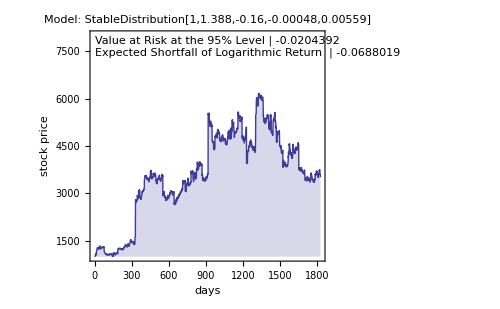

```mathematica
ListLinePlot[1000 Exp[Accumulate[logReturns]],PlotRange->{1000,8000},PlotLabel->Framed[Style[Row[{"Model:  ",log𝒟}],14],BaseStyle->{FontFamily->"Verdana"},Background->Lighter[Blend[{Yellow,Orange}],0.7],RoundingRadius->2],Frame->{{True,False},{True,False}},FrameLabel->{{Style["stock price",Bold,12],""},{Style["days",Bold,12],""}},Filling->Axis,Epilog->Inset[Framed[Grid[{{"Value at Risk at the 95% Level",VaR=InverseSurvivalFunction[log𝒟,0.95]},{"Expected Shortfall of Logarithmic Return ",NExpectation[x\[Conditioned]x<VaR,x\[Distributed]log𝒟]}},ItemSize->{{11,6},2},Background->{None,{{Lighter[Blend[{Red,Blue}],.8],Lighter[Blend[{Green,Blue}],.8]}}}],RoundingRadius->10],{0,8000},{Left,Top}],ImageSize->500]
```